# Portfolio Optimization

## Asset definitions

We define the assets that are going to be used. In this example, they were chosen among the top 10 performing stocks in S&P.

```mathematica
(*"AAPL","MSFT","AMZN","JNJ","XOM","JPM","GOOG"*)
(*"FAS","FIW","FYX","ERY","GEX","PSP"*)
portfolio={"AAPL","MSFT","AMZN","JNJ","XOM","JPM","GOOG"};
```

We get the pricing data by specifying 2010/01/01 as a starting date and then proceed to plot it.

```mathematica
data=FinancialData[#,"Price",{2010,1,1}]&/@portfolio;
```

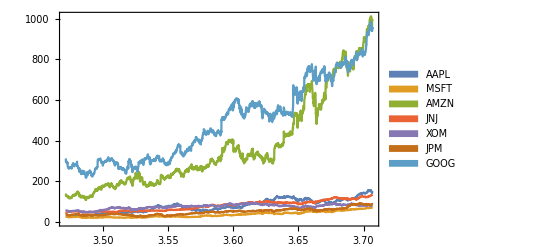

```mathematica
DateListPlot[data, PlotRange->All,Joined->True, PlotLegends->SwatchLegend[portfolio]]
```

```mathematica
usefulData=FinancialData[#,"Close",{2010,1,1},"Value"]&/@portfolio;
```

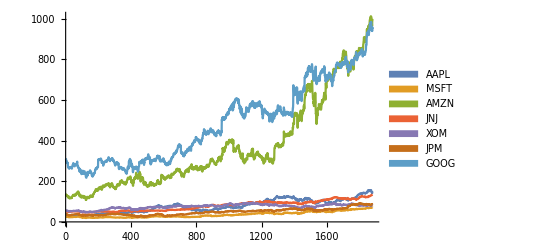

```mathematica
ListPlot[usefulData,PlotRange->All,Joined->True,PlotLegends->SwatchLegend[portfolio]]
```

## Returns

What we are interested in are returns, that is, the percentage change of each asset price with respect to the one of the previous trading day.

```mathematica
getReturns[lst_]:=(lst[[#+1]]/lst[[#]])-1&/@Range[Length[lst]-1];
```

```mathematica
returns=getReturns[usefulData[[#]]]&/@Range[Length[portfolio]];
```

Having calculated the returns with the defined function, we can proceed to plot the data.

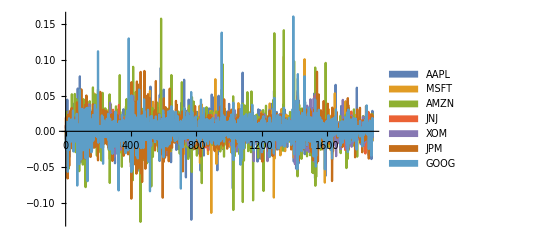

```mathematica
ListPlot[returns,PlotRange->All,Joined->True,PlotLegends->SwatchLegend[portfolio]]
```

## Optimization

Now that we have calculated returns, we can proceed to optimize our portfolio; that is, find a set of  weights (one for each asset) w, such that the expected risk of the portfolio is minimized for a given expected return. For this, we use modern portfolio theory, in particular, Markowitz optimization.

We can first define the weights vector as a symbolic object with the corresponding assets as subscripts.

```mathematica
weights=Transpose[{Subscript[w,#]&/@portfolio}]
```

{{w_AAPL},{w_MSFT},{w_AMZN},{w_JNJ},{w_XOM},{w_JPM},{w_GOOG}}

The expected return of our portfolio is given by R = ∑ m · w, where m is a row vector whose entries are given by the mean of each asset’s returns.

```mathematica
meanRet={Mean[#]&/@returns};
portfolioMean=Flatten[meanRet.weights][[1]]*252;
```

Next we calculate the variance of our portfolio, given by var = w^T · C · w, where C is the covariance matrix of the returns.

```mathematica
covMat=Covariance[Transpose[returns]];
portfolioVar=Flatten[Transpose[weights].covMat.weights][[1]]*252;
```

We multiply our results by 252 to consider annual returns, since there are approximately 252 business days in a year.

### Constraints

Having arranged our data, we need to specify some constraints on the optimization so that the result makes sense in a real investing environment, as well as to provide a way to personalize the optimization process. There are three basic constraints which we are interested on:

∑_i w_i=1

The following function combines these constraints into a single constraint list, which we can then pass to the optimization function.

```mathematica
constraints[wl_,wg_,retMin_]:=Union[
GreaterEqualThan[wl][#]&/@Flatten[Transpose[weights]],
LessEqualThan[wg][#]&/@Flatten[Transpose[weights]],
List[Total[weights][[1]]==1],
List[GreaterEqualThan[retMin][portfolioMean]]
];
```

```mathematica
optPort[x_,y_,z_]:=NMinimize[{portfolioVar,constraints[x,y,z]},Flatten[weights]];
```

```mathematica
mv=optPort[0.05, 0.25, 0.0]
expRetRisk={Sqrt[mv[[1]]],portfolioMean /.mv[[2]]}
```

{0.0217333,{w_AAPL→0.140274,w_MSFT→0.15524,w_AMZN→0.05,w_JNJ→0.25,w_XOM→0.25,w_JPM→0.05,w_GOOG→0.104486}}

{0.147422,0.155526}

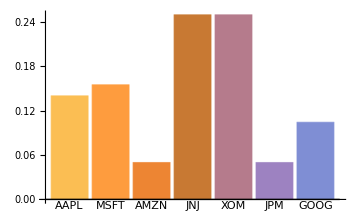

```mathematica
BarChart[{Last[mv[[2,#]]]&/@Range[Length[portfolio]]},ImageSize->Medium,ChartLabels->portfolio]
```

```mathematica
effFrontier=Table[
{
NMinimize[
{
Sqrt[portfolioVar],
Union[
GreaterEqualThan[0.05][#]&/@Flatten[Transpose[weights]],
LessEqualThan[0.25][#]&/@Flatten[Transpose[weights]],
List[Total[weights][[1]]==1],
List[Equal[portfolioMean,i]]
]
},Flatten[weights]
][[1]],i
},{i,0.0,1,.001}];//Quiet
```

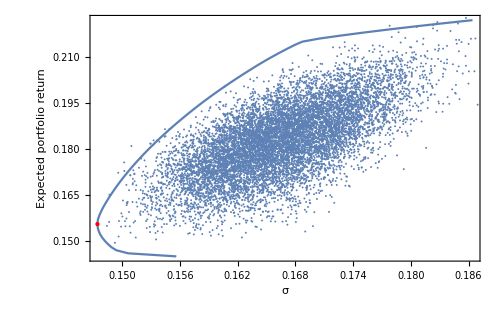

```mathematica
Show[ListLinePlot[effFrontier,Epilog->{Red,PointSize->Large,Point[expRetRisk]},Frame->True,FrameLabel->{"σ","Expected portfolio return"},PlotRange->{Automatic,Automatic},BaseStyle->14,ImageSize->500],ListPlot[Table[{Sqrt[portfolioVar],portfolioMean}/.Thread[Flatten[Transpose[weights]]->#/Total[#]&[RandomReal[{.05,0.25},Length[portfolio]]]],{10000}]]]//Quiet
```